```mathematica
SetDirectory["~/Projects/Paths/control/main/output/genf_z"];
```

```mathematica
inputs={Import["out_files"]}//Flatten;
pars=Import["pars.dat"]//Flatten;
```

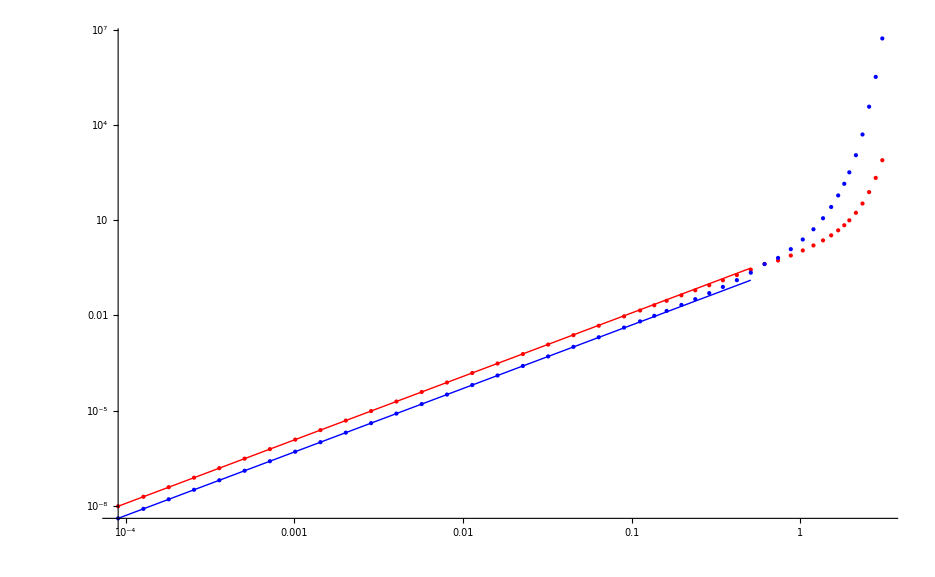

```mathematica
ClearAll;
Clear[cumsVSavjmp,plots];
cumsVSavjmp={};
plots={};
Do[
Clear[cums,mean,var];
cums={pars[[i]],mean,var};
data=Import[inputs[[i]]];
smin=First[data][[1]];
smax=Last[data][[1]];
genfexp=mean*s+1/2*var*s^2;
cumsVSavjmp=Append[cumsVSavjmp, cums/.FindFit[data,genfexp,{mean,var},s]];
plots=Append[plots,Show[ListPlot[data,Filling->Axis,Joined->True,PlotStyle->Red],Plot[genfexp,{s,smin,smax}]]];
,{i,Length[pars]}]
means=Table[{cumsVSavjmp[[i]][[1]],cumsVSavjmp[[i]][[2]]},{i,Length[cumsVSavjmp]}];
vars=Table[{cumsVSavjmp[[i]][[1]],cumsVSavjmp[[i]][[3]]},{i,Length[cumsVSavjmp]}];
points=ListLogLogPlot[{means,vars},PlotStyle->{Red,Blue}];
fits=LogLogPlot[{BesselJZero[0,1]/2*x^2,x^2/2},{x,pars[[1]],pars[[30]]},PlotStyle->{{Red,Thin},{Blue,Thin}}];
Show[{points,fits}]
Export["meanANDvar.dat",cumsVSavjmp];
```